This notebook imports dat files, and plots energy eigenvalues and LDoS of projected QAHI

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
datFileEnergylocation="/data/hstci/dislocation/energies/";
datFileLDOSlocation="/data/hstci/dislocation/LDOS/";
datfilePBCName="t0=1.0_t=1.0_t_prime=-1.5_m_0=3.0_x_periodic=1_y_periodic=1_L=100_l1=25_l2=50_mlattice=50_m=0.6180339887498949_c1=-12_c2=-2";
datfileOBCName="t0=1.0_t=1.0_t_prime=-1.5_m_0=-3.0_x_periodic=1_y_periodic=1_L=100_l1=25_l2=50_mlattice=50_m=0.6180339887498949_c1=-12_c2=-2";
```

```mathematica
StringJoin[datFileEnergylocation,datfilePBCName];
```

```mathematica
Clear[dataEnergyPBC,dataEnergyOBC]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataEnergyPBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfilePBCName,".csv"]]];
```

```mathematica
dataEnergyOBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".csv"]]];
```

```mathematica
Clear[Lattice];
```

```mathematica
Lattice=Table[{j,0},{j,1,Dimensions[dataEnergyOBC][[1]]/2}];
```

```mathematica
largestX = Dimensions[Lattice][[1]]
```

888

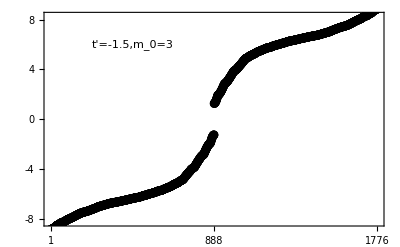

```mathematica
plt1=Show[
ListPlot[dataEnergyPBC,Frame-> True,Axes-> False,PlotRange-> {{0,2*largestX},{-8.25,8.25}},PlotStyle-> {Black,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-8,-4,0,4,8},None},{{1,largestX,2*largestX},None}},BaseStyle-> 18],

(*Plot[2.0,{x,0.5*largestX-350,0.5*largestX-200},PlotStyle-> {Thick,Black}],*)

Epilog-> {Inset["t'=-1.5,m_0=3",{0.5*largestX,6}]}
]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfilePBCName,".pdf"],plt1];
```

```mathematica
OBCRED=Select[dataEnergyOBC,-0.1<=#<=0.1&]
```

{-6.36587×10^-6}

```mathematica
OBCRED={largestX,OBCRED[[1]]}
```

{888,-6.36587×10^-6}

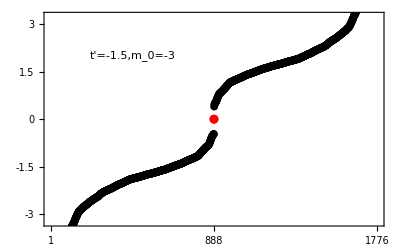

```mathematica
plt0=Show[ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{0,2*largestX},{-3.25,3.25}},PlotStyle-> {Black,PointSize[0.014]},
FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-3,-1.5,0,1.5,3},None},{{1,largestX,2*largestX},None}},BaseStyle-> 18],
(*Plot[2.0,{x,0.5*largestX-350,0.5*largestX-200},PlotStyle-> {Thick,Red}],*)
ListPlot[{OBCRED},PlotStyle->{Red,PointSize[0.016]}],
Epilog-> {Inset["t'=-1.5,m_0=-3",{0.5*largestX,2.0}]}
]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".pdf"],plt0];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataLDoSPBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfilePBCName,".csv"]]];
```

```mathematica
dataLDoSPBC=Table[{nn,0,dataLDoSPBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
dataLDoSOBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".csv"]]];
```

```mathematica
dataLDoSOBC=Table[{nn,0,dataLDoSOBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
Dimensions[dataLDoSOBCdat]
```

{888}

```mathematica
largestX
```

888

```mathematica
rngOld={0,Max[#]}&@dataLDoSOBC[[All,3]]
```

{0,0.198068}

```mathematica
rng={0,0.22}
```

{0,0.22}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"0.028"},{rng[[2]]-10^-3,"0.056"}}]
```

```mathematica
(** Crop the image appropriately and put the numbers in inkscape **)
```

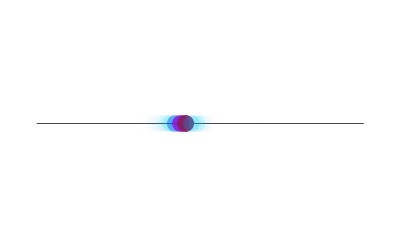

```mathematica
plt2=Show[
ListPlot[Lattice,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {All,{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@dataLDoSOBC,
BaseStyle-> 18
]

]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".pdf"],plt2];
```

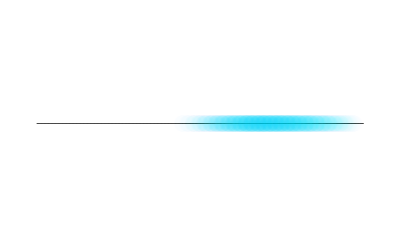

```mathematica
plt3=Show[
ListPlot[Lattice,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {All,{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@dataLDoSPBC,
BaseStyle-> 18
]

]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfilePBCName,".pdf"],plt3];
```